```mathematica
efficiency=0.6;
eventReq=Sqrt[11.8];
```

```mathematica
readRatesAndNs[projectName_String, luminosity_?NumericQ]:=Module[{rate, ns},rate=Module[{files=FileNames["../"<>projectName<>"/root_analysis/tables/*.dat"],rateLists,rates,interpolationData},rateLists=Map[ReadList[#,{Number,Number,Number}]&,files];
rates=Flatten[rateLists,1];
interpolationData=rates/.{m_,t_,r_}->{{m,Log[t]},r};
Interpolation[interpolationData]];
ns=Interpolation[ReadList["../"<>projectName<>"/madgraph/xs.dat",{Number,Number}]/.{m_,xs_}->{m,Log[xs luminosity]}];
{rate, ns}]
```

```mathematica
{ratesCurr, nsCurr} = readRatesAndNs["disappearing-mindm-curr-lhc", 36];
```

```mathematica
{ratesHL, nsHL} = readRatesAndNs["disappearing-mindm-hl-lhc", 3000];
```

```mathematica
{rates100, ns100} = readRatesAndNs["disappearing-mindm-100TeV", 3000];
```

InterpolatingFunction::dmval: Input value {100.06,-2.30252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

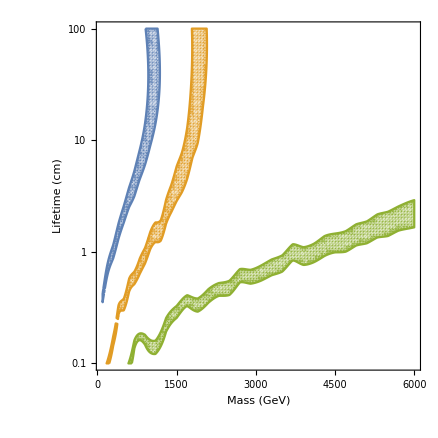

```mathematica
output=RegionPlot[
{
eventReq > 10^3*efficiency*Exp[nsCurr[m]] ratesCurr[m,lt]>1.,
(m < 3000 && eventReq > 10^3*efficiency*Exp[nsHL[m]] ratesHL[m,lt]>1),
 eventReq > 10^3*efficiency*Exp[ns100[m]] rates100[m,lt]>1
},{m,100,6000},{lt,Log[0.1],Log[100]},FrameLabel->{"Mass (GeV)","Lifetime (cm)"},FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],None},Automatic}, PlotPoints->100]
```

```mathematica
mZ =91.2;
mW =80.4;
sW2 = 1 - (mW / mZ)^2; 
v = 246;
alpha2 = (2 mW / v)^2/ (4π);
f[r_] := r (2 r^3 Log[r] - 2 r + √(r^2 - 4)(r^2 + 2) Log[(r^2 - 2 - r √(r^2 - 4))/2])/2
fExpd[r_] := Module[{rp},(Normal[Series[f[rp], {rp, 0, 10}, Assumptions->rp>0]])/. rp-> r]
Δm[m_?NumericQ] := (alpha2 m)/(4π)(sW2 fExpd[mZ/m] + fExpd[mW/m] -fExpd[mZ/m] )
gam[dm_?NumericQ] := 6/2(dm/0.166)^3 √(3.346(1 - 0.135^2/dm^2))1/5.6
```

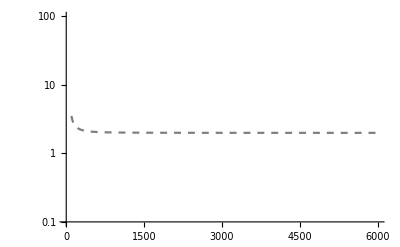

```mathematica
outputLT=LogPlot[
{
1/gam[Δm[m]]
},{m,100,6000},FrameLabel->{"Mass (GeV)","Lifetime (cm)"},PlotRange->{0.1,100}, PlotStyle->Directive[Dashed, Gray]]
```

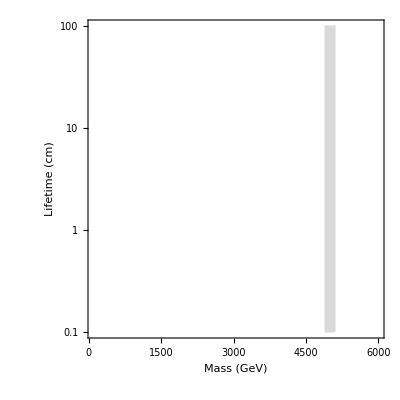

```mathematica
outputAb=RegionPlot[
{
5100 > m > 4900
},{m,100,6000},{lt,Log[0.1],Log[100]},FrameLabel->{"Mass (GeV)","Lifetime (cm)"},FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],None},Automatic},PlotStyle->LightGray,BoundaryStyle->{Thick, LightGray}]
```

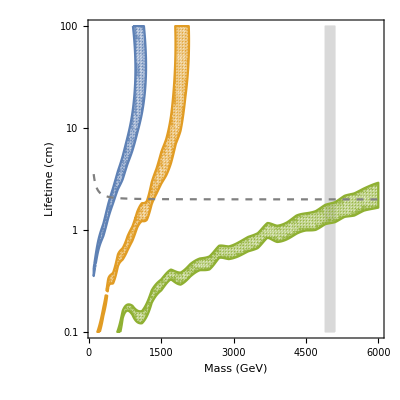

```mathematica
Show[outputAb,output, outputLT]
```

```mathematica
Export["./excludedRegion.pdf",output]
```